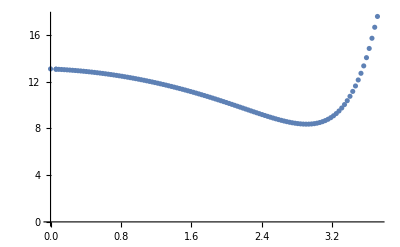

```mathematica
h={{0,13.084549},{0.062500,13.059762},{0.062500,13.059762},{0.093750,13.046440},{0.125000,13.032294},{0.156250,13.017243},{0.187500,13.001230},{0.218750,12.984217},{0.250000,12.966176},{0.281250,12.947087},{0.312500,12.926935},{0.343750,12.905708},{0.375000,12.883398},{0.406250,12.859998},{0.437500,12.835502},{0.468750,12.809907},{0.500000,12.783209},{0.531250,12.755405},{0.562500,12.726494},{0.593750,12.696474},{0.625000,12.665344},{0.656250,12.633101},{0.687500,12.599746},{0.718750,12.565277},{0.750000,12.529694},{0.781250,12.492996},{0.812500,12.455184},{0.843750,12.416255},{0.875000,12.376211},{0.906250,12.335051},{0.937500,12.292776},{0.968750,12.249384},{1.000000,12.204877},{1.031250,12.159254},{1.062500,12.112516},{1.093750,12.064663},{1.125000,12.015696},{1.156250,11.965615},{1.187500,11.914422},{1.218750,11.862117},{1.250000,11.808702},{1.281250,11.754178},{1.312500,11.698547},{1.343750,11.641812},{1.375000,11.583974},{1.406250,11.525037},{1.437500,11.465005},{1.468750,11.403882},{1.500000,11.341673},{1.531250,11.278385},{1.562500,11.214023},{1.593750,11.148597},{1.625000,11.082116},{1.656250,11.014591},{1.687500,10.946035},{1.718750,10.876465},{1.750000,10.805897},{1.781250,10.734353},{1.812500,10.661856},{1.843750,10.588434},{1.875000,10.514118},{1.906250,10.438945},{1.937500,10.362956},{1.968750,10.286199},{2.000000,10.208729},{2.031250,10.130605},{2.062500,10.051897},{2.093750,9.972683},{2.125000,9.893051},{2.156250,9.813097},{2.187500,9.732932},{2.218750,9.652676},{2.250000,9.572464},{2.281250,9.492445},{2.312500,9.412784},{2.343750,9.333663},{2.375000,9.255282},{2.406250,9.177859},{2.437500,9.101636},{2.468750,9.026876},{2.500000,8.953869},{2.531250,8.882931},{2.562500,8.814408},{2.593750,8.748676},{2.625000,8.686151},{2.656250,8.627281},{2.687500,8.572562},{2.718750,8.522532},{2.750000,8.477781},{2.781250,8.438954},{2.812500,8.406757},{2.843750,8.381964},{2.875000,8.365422},{2.906250,8.358062},{2.937500,8.360905},{2.968750,8.375073},{3.000000,8.401804},{3.031250,8.442456},{3.062500,8.498529},{3.093750,8.571678},{3.125000,8.663728},{3.156250,8.776692},{3.187500,8.912791},{3.218750,9.074460},{3.250000,9.264362},{3.281250,9.485365},{3.312500,9.740502},{3.343750,10.032845},{3.375000,10.365283},{3.406250,10.740196},{3.437500,11.159316},{3.468750,11.624481},{3.500000,12.139121},{3.531250,12.708840},{3.562500,13.341247},{3.593750,14.045734},{3.625000,14.832089},{3.656250,15.704809},{3.687500,16.645385},{3.718750,17.568840}};
ListPlot[h]
```

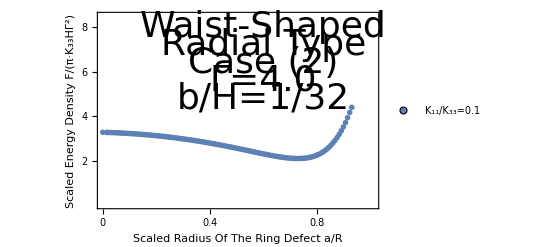

```mathematica
gg=h*Table[{0.25,4/16},{i,0,119}];
ListPlot[{gg},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{2,4,6,8},None},{{0,0.2, 0.4, 0.6, 0.8,1.0},None}}, PlotRange->{{0,1.01},{0,8.5}},FrameLabel->{{"Scaled Energy Density F/(π·K_33HΓ^2)", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=0.1","K_11/K_33=2.0","K_11/K_33=3.0","K_11/K_33=4.0"},LegendMarkers->{{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12}}],{Left, Top}],Epilog->{Text[Style["Waist-Shaped",Directive[Black,36]],{0.6,8}],Text[Style["Radial Type",Directive[Black,36]],{0.6,7.2}],Text[Style["Case (2)",Directive[Black,36]],{0.6,6.4}],Text[Style["Γ=4.0",Directive[Black,36]],{0.6,5.6}],Text[Style["b/H=1/32",Directive[Black,36]],{0.6,4.8}]}]
```